```mathematica
$Assumptions={X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈
Reals}
```

{X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,Null,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈Reals}

```mathematica
cXStart=-100;
cXStep=0.1;
cXLength= 2000;
cTStep="1.0e-4";
cTStepint = 0.00001;
cTLength="1000000";
cTLengthint=1000000;
cep=0.60;
ccuts=10;
csigma=1;
cdslit=3.0;
```

```mathematica
√((h^2 t^2)/(4 σ^2)+σ^2)
```

√((h^2 t^2)/(4 σ^2)+σ^2)

```mathematica
twidth[h_,t_,σ_]:=√((h^2 t^2)/(4 σ^2)+σ^2)
```

```mathematica
Rfnew[x_,t_,d_,σ_,h_]=(σ ((ⅇ^(-(d-x)^2/(4 twidth[h,t,σ]^2))+ⅇ^(-(d+x)^2/(4 twidth[h,t,σ]^2)))^2-4 ⅇ^(-(d^2+x^2)/(2 twidth[h,t,σ]^2)) Sin[(h d t x)/(4 twidth[h,t,σ]^2 σ^2)]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) twidth[h,t,σ])
```

(σ ((ⅇ^(-(d-x)^2/(4 ((h^2 t^2)/(4 σ^2)+σ^2)))+ⅇ^(-(d+x)^2/(4 ((h^2 t^2)/(4 σ^2)+σ^2))))^2-4 ⅇ^(-(d^2+x^2)/(2 ((h^2 t^2)/(4 σ^2)+σ^2))) Sin[(d h t x)/(4 σ^2 ((h^2 t^2)/(4 σ^2)+σ^2))]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √((h^2 t^2)/(4 σ^2)+σ^2))

```mathematica
animttt = Table[GraphicsGrid[{{Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[0.0]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[0.02]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]},{Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[0.05]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[0.2]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]},{Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[0.6]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), t ,cdslit,csigma,Sqrt[1.0]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]}}],{t,0, 20,0.2}];
```

```mathematica
Export["ScaledSchrodAni.mov",animttt]
```

ScaledSchrodAni.mov

```mathematica
ListAnimate[animttt]
```

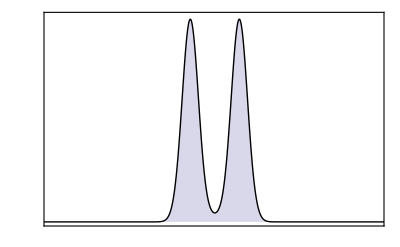

```mathematica
Plot[Rfnew[(x-cXStep), 0 ,cdslit,csigma,Sqrt[0.0]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]
```

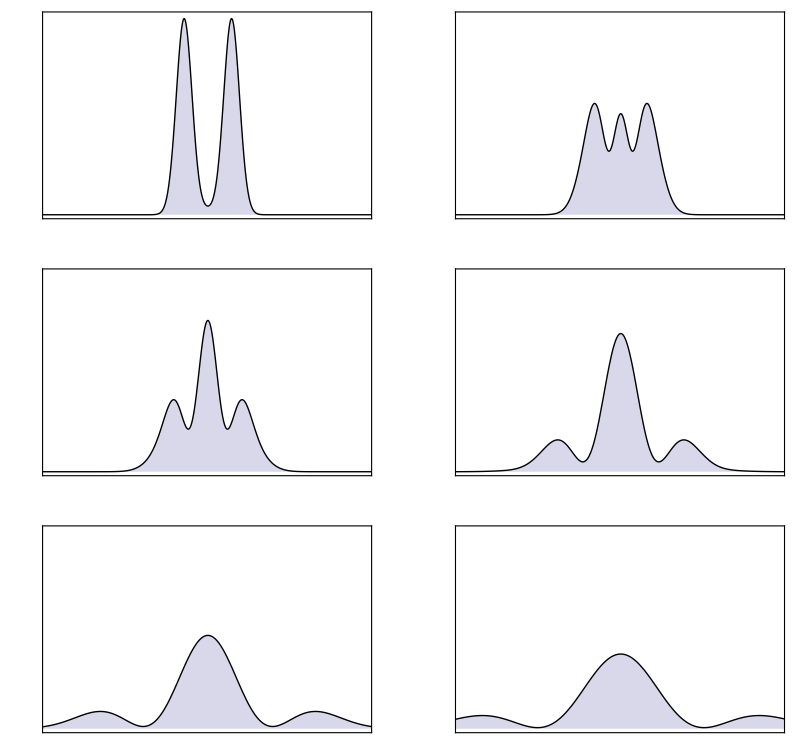

```mathematica
GraphicsGrid[{{Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[0.0]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[0.02]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]},{Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[0.05]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[0.2]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]},{Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[0.6]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],Plot[Rfnew[(x-cXStep), 20 ,cdslit,csigma,Sqrt[1.0]],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-20,20},{0,0.2}}, PlotPoints->100,PlotStyle->Black,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis]}}]
```